```mathematica
RK4[f_,fpar_,{t0_,tn_},x0_,steps_]:=Module[{told=t0,xold=x0,tnew,xnew,k1,k2,k3,k4,sollist={{t0,x0}},h},
h=N[(tn-t0)/steps];
Do[tnew=told+h;
k1=f[told,xold,fpar];
k2=f[told+h/2,xold+h*k1/2,fpar];
k3=f[told+h/2,xold+h*k2/2,fpar];
k4=f[told+h,xold+h*k3,fpar];
xnew=xold+h*(k1/6+k2/3+k3/3+k4/6);
sollist=Append[sollist,{tnew,xnew}];
told=tnew;
xold=xnew,
steps];
Return[sollist]]

RK4dynamicstep[f_,fpar_,{t0_,tn_},x0_,steps_]:=Module[{told=t0,xold=x0,tnew,xnew,k1,k2,k3,k4,sollist={{t0,x0}},h,recurs},
h=N[(tn-t0)/steps];
Do[tnew=told+h;
k1=f[told,xold,fpar];
k2=f[told+h/2,xold+h*k1/2,fpar];
k3=f[told+h/2,xold+h*k2/2,fpar];
k4=f[told+h,xold+h*k3,fpar];
xnew=xold+h*(k1/6+k2/3+k3/3+k4/6);
If[Im[xnew]≠Im[xold],
recurs=RK4dynamicstep[f,fpar,{told,tnew},xold,2];
xnew=recurs[[3]][[2]]; (*takes last step of a 2 step integration*)
,];
sollist=Append[sollist,{tnew,xnew}];
told=tnew;
xold=xnew,
steps];
sollist]

FFT[invec_]:= Module[{ elist, olist, netlist, eft, oft, n, omega},
If[Length[invec]== 1, (*shamelessly ripped out of joel's fft chapter, identical except for my aesthetic preference for Do over For*)
Return[invec];];
n= Length[invec];
omega = 1;
elist = Table[invec[[j]], {j, 1, n, 2}];
olist=  Table[invec[[j]], {j, 2, n, 2}];
eft =FFT[elist];
oft = FFT[olist];
netlist = Table[0,{j, 0, n -1}];
Do[netlist[[k + 1]]= eft[[k + 1]]+ omega oft[[k + 1]];
netlist[[k + n/2 + 1]]= eft[[k+1]]- omega oft[[k + 1]];
omega = omega Exp[2 Pi I/n];
,{k,n/2}];
Return[netlist];];
```

```mathematica
|
```

```mathematica
(*not sure if this works properly?*)
RelMomentumFinder[txv_]:= Module[{totmom=0},Do[totmom+=(txv[[2]][[1]][[i]][[1]]*txv[[2]][[2]][[i]][[2]]-txv[[2]][[1]][[i]][[2]]*txv[[2]][[2]][[i]][[1]])/Sqrt[1-txv[[2]][[2]][[i]].txv[[2]][[2]][[i]]],{i,Length[txv]}];
Return[totmom]
];
(*Pass in rk4output[[i]] and get p/m*)
RelE[txv_,con_]:= Module[{totE=0},Do[totE+=1/Sqrt[1-txv[[2]][[2]][[i]].txv[[2]][[2]][[i]]]-1;
Do[If[con[[i]][[j]]!=0,
totE+=(Sqrt[(txv[[2]][[1]][[i]]-txv[[2]][[1]][[j]]).(txv[[2]][[1]][[i]]-txv[[2]][[1]][[j]])]-con[[i]][[j]])^2/2,]
,{j,i,Length[con]}]
,{i,Length[con]}];
Return[totE]
];
```

```mathematica
Length[RelDisc4[[2]][[2]][[1]]]
```

512

```mathematica
f[i_]:= 2Pi*i;
initial[N_]:=Module[{x=Array[f,N],l=Array[zero,N]},
Return[{x/N,l}]];
zero[x_]:=0;

maattricks[i_,j_,N_]:=If[i==j,-2,
If[Abs[i-j]==1||Abs[Mod[i,N]-Mod[j,N]]==1,1,0]];
mattricksy[N_]:=Function[{i,j},maattricks[i,j,N]];
nonrelRing[n_]:=Function[{t,x,alpha}, (*This is where I think I should add t_r in th*)
Module[{k=Array[mattricksy[n],{n,n}],xnu=Array[initial,n],temp=Array[Function[l,If[l==1,-2Pi,If[l==n,2Pi,0]]],n]},
xnu=alpha(x[[1]].k+temp); (*temp here is a somewhat slapdash solution that nonetheless should work as long as the masses aren't too slonky*)
{x[[2]],Chop[N[xnu]]}
]]
```

```mathematica
relRing[n_,wc_]:=Function[{t,x,alpha}, 
Module[{k=Array[mattricksy[n],{n,n}],xnu=Array[initial,n],temp=Array[Function[l,If[l==1,-2Pi,If[l==n,2Pi,0]]],n]},
xnu=alpha(x[[1]].k+temp)*(1-x[[2]]*x[[2]]/wc^2)^(3/2); (*temp here is a somewhat slapdash solution that nonetheless should work as long as the masses aren't too slonky*)
{x[[2]],Chop[N[xnu]]}
]]
relRingTorked[n_,wc_,tork_]:=Function[{t,x,alpha}, 
Module[{k=Array[mattricksy[n],{n,n}],xnu=Array[initial,n],temp=Array[Function[l,If[l==1,-2Pi,If[l==n,2Pi,0]]],n]},
xnu=(alpha(x[[1]].k+temp)+tork)*(1-x[[2]]*x[[2]]/wc^2)^(3/2); (*temp here is a somewhat slapdash solution that nonetheless should work as long as the masses aren't too slonky*)
{x[[2]],Chop[N[xnu]]}
]]
disque[n_,wc_,connectionmatrix_] := Function[{t,x,alpha},
Module[{(*k=Table[x[[2]][[i]].x[[2]][[i]],{i,Length[x[[2]]]},2],*)xnu=Table[0,n,2],fx=0,fy=0,r=0},(*each of these needs to also store their rest lengths, so this form actually donut work*)
Do[ (*runs through connected points and adds forces in x/y direc. for each *)
fx=0;
fy=0;
Do[
If[i≠j&&connectionmatrix[[i]][[j]]≠0,
r=Sqrt[(x[[1]][[i]]-x[[1]][[j]]).(x[[1]][[i]]-x[[1]][[j]])];
fx+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[1]]-x[[1]][[j]][[1]])/r;(*second term should be eq. to cos*)
fy+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[2]]-x[[1]][[j]][[2]])/r;(*second term should be eq. to sin*)
,r;
];
xnu[[i]]={fx,fy}*(1-(x[[2]][[i]].x[[2]][[i]])/wc^2)^(3/2) (*hopefully the boost factr doesn't change in 2d*)
,{j,n}]
,{i,n}]; (*potential problem child*)
{x[[2]],Chop[N[xnu]]}
]]

torqueDisque[n_,wc_,connectionmatrix_,torque_] := Function[{t,x,alpha},
Module[{(*k=Table[x[[2]][[i]].x[[2]][[i]],{i,Length[x[[2]]]},2],*)xnu=Table[0,n,2],fx=0,fy=0,r=0},(*each of these needs to also store their rest lengths, so this form actually donut work*)
Do[ (*runs through connected points and adds forces in x/y direc. for each *)
fx=0;
fy=0;
Do[
If[i≠j&&connectionmatrix[[i]][[j]]≠0,
r=Sqrt[(x[[1]][[i]]-x[[1]][[j]]).(x[[1]][[i]]-x[[1]][[j]])];
fx+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[1]]-x[[1]][[j]][[1]])/r;(*second term should be eq. to cos*)
fy+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[2]]-x[[1]][[j]][[2]])/r;(*second term should be eq. to sin*)
fx+=torque(-x[[1]][[i]][[2]])/r^2;
fy+=torque(x[[1]][[i]][[1]])/r^2;
,r;
];
xnu[[i]]={fx,fy}*(1-(x[[2]][[i]].x[[2]][[i]])/wc^2)^(3/2) (*hopefully the boost factr doesn't change in 2d*)
,{j,n}]
,{i,n}]; (*potential problem child*)

{x[[2]],Chop[N[xnu]]}
]]

torqueDisqueCutoff[n_,wc_,connectionmatrix_,torque_,cutofft_] := Function[{t,x,alpha},
Module[{(*k=Table[x[[2]][[i]].x[[2]][[i]],{i,Length[x[[2]]]},2],*)xnu=Table[0,n,2],fx=0,fy=0,r=0},(*each of these needs to also store their rest lengths, so this form actually donut work*)
Do[ (*runs through connected points and adds forces in x/y direc. for each *)
fx=0;
fy=0;
Do[
If[i≠j&&connectionmatrix[[i]][[j]]≠0,
r=Sqrt[(x[[1]][[i]]-x[[1]][[j]]).(x[[1]][[i]]-x[[1]][[j]])];
fx+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[1]]-x[[1]][[j]][[1]])/r;(*second term should be eq. to cos*)
fy+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[2]]-x[[1]][[j]][[2]])/r;(*second term should be eq. to sin*)
fx+=HeavisideTheta[t-cutofft]torque(-x[[1]][[i]][[2]])/r^2;
fy+=HeavisideTheta[t-cutofft]torque(x[[1]][[i]][[1]])/r^2;
,r;
];
xnu[[i]]={fx,fy}*(1-(x[[2]][[i]].x[[2]][[i]])/wc^2)^(3/2) (*hopefully the boost factr doesn't change in 2d*)
,{j,n}]
,{i,n}]; (*potential problem child*)

{x[[2]],Chop[N[xnu]]}
]]


nDimtorqueDisqueCutoff[n_,connectionmatrix_,torque_,cutofft_] := Function[{t,x,alpha},
Module[{(*k=Table[x[[2]][[i]].x[[2]][[i]],{i,Length[x[[2]]]},2],*)xnu=Table[0,n,2],fx=0,fy=0,r=0},(*each of these needs to also store their rest lengths, so this form actually donut work*)
Do[ (*runs through connected points and adds forces in x/y direc. for each *)
fx=0;
fy=0;
Do[
If[i≠j&&connectionmatrix[[i]][[j]]≠0,
r=Sqrt[(x[[1]][[i]]-x[[1]][[j]]).(x[[1]][[i]]-x[[1]][[j]])];
fx+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[1]]-x[[1]][[j]][[1]])/r;(*second term should be eq. to cos*)
fy+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[2]]-x[[1]][[j]][[2]])/r;(*second term should be eq. to sin*)
fx+=HeavisideTheta[cutofft-t]torque(-x[[1]][[i]][[2]])/r^2;
fy+=HeavisideTheta[cutofft-t]torque(x[[1]][[i]][[1]])/r^2;
,r;
];
xnu[[i]]={fx,fy}*(1-(x[[2]][[i]].x[[2]][[i]]))^(3/2) (*hopefully the boost factr doesn't change in 2d*)
,{j,n}]
,{i,n}]; (*potential problem child*)

{x[[2]],Chop[N[xnu]]}
]]

nDimtorqueAxleCutoff[n_,connectionmatrix_,torque_,cutofft_,oR_,iR_] := Function[{t,x,alpha},
Module[{(*k=Table[x[[2]][[i]].x[[2]][[i]],{i,Length[x[[2]]]},2],*)xnu=Table[0,n,2],fx=0,fy=0,iC=n (iR/oR)^2},(*each of these needs to also store their rest lengths, so this form actually donut work*)
Do[ (*runs through connected points and adds forces in x/y direc. for each *)
fx=0;
fy=0;
Do[
If[i≠j&&connectionmatrix[[i]][[j]]≠0,
r=Sqrt[(x[[1]][[i]]-x[[1]][[j]]).(x[[1]][[i]]-x[[1]][[j]])];
fx+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[1]]-x[[1]][[j]][[1]])/r;(*second term should be eq. to cos*)
fy+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[2]]-x[[1]][[j]][[2]])/r;(*second term should be eq. to sin*)
If[i<= iC,
fx+=HeavisideTheta[cutofft-t]torque(-x[[1]][[i]][[2]])/r^2;
fy+=HeavisideTheta[cutofft-t]torque(x[[1]][[i]][[1]])/r^2;,
];
,r;
];
xnu[[i]]={fx,fy}*(1-(x[[2]][[i]].x[[2]][[i]]))^(3/2) (*hopefully the boost factr doesn't change in 2d*)
,{j,n}]
,{i,n}]; (*potential problem child*)

{x[[2]],Chop[N[xnu]]}
]];

nDimtorqueRimCutoff[n_,connectionmatrix_,torque_,cutofft_,oR_,iR_] := Function[{t,x,alpha},
Module[{(*k=Table[x[[2]][[i]].x[[2]][[i]],{i,Length[x[[2]]]},2],*)xnu=Table[0,n,2],fx=0,fy=0,r=0,iC=n (iR/oR)^2},(*each of these needs to also store their rest lengths, so this form actually donut work*)
Do[ (*runs through connected points and adds forces in x/y direc. for each *)
fx=0;
fy=0;
Do[
If[i≠j&&connectionmatrix[[i]][[j]]≠0,
r=Sqrt[(x[[1]][[i]]-x[[1]][[j]]).(x[[1]][[i]]-x[[1]][[j]])];
fx+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[1]]-x[[1]][[j]][[1]])/r;(*second term should be eq. to cos*)
fy+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[2]]-x[[1]][[j]][[2]])/r;(*second term should be eq. to sin*)
If[i≥ iC,
fx+=HeavisideTheta[cutofft-t]torque(-x[[1]][[i]][[2]])/r^2;
fy+=HeavisideTheta[cutofft-t]torque(x[[1]][[i]][[1]])/r^2;,
];
,r;
];
xnu[[i]]={fx,fy}*(1-(x[[2]][[i]].x[[2]][[i]]))^(3/2) (*hopefully the boost factr doesn't change in 2d*)
,{j,n}]
,{i,n}]; (*potential problem child*)

{x[[2]],Chop[N[xnu]]}
]];

nDimtorqueRimGenCutoff[n_,connectionmatrix_,torque_,cutofft_,rim_] := Function[{t,x,alpha},
Module[{(*k=Table[x[[2]][[i]].x[[2]][[i]],{i,Length[x[[2]]]},2],*)xnu=Table[0,n,2],fx=0,fy=0,r=0},(*each of these needs to also store their rest lengths, so this form actually donut work*)
Do[ (*runs through connected points and adds forces in x/y direc. for each *)
fx=0;
fy=0;
Do[
If[i≠j&&connectionmatrix[[i]][[j]]≠0,
r=Sqrt[(x[[1]][[i]]-x[[1]][[j]]).(x[[1]][[i]]-x[[1]][[j]])];
fx+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[1]]-x[[1]][[j]][[1]])/r;(*second term should be eq. to cos*)
fy+=(connectionmatrix[[i]][[j]]-r)*(x[[1]][[i]][[2]]-x[[1]][[j]][[2]])/r;(*second term should be eq. to sin*)
If[rim[[i]]==True,
fx+=HeavisideTheta[cutofft-t]torque(-x[[1]][[i]][[2]])/r^2;
fy+=HeavisideTheta[cutofft-t]torque(x[[1]][[i]][[1]])/r^2;,
];
,r;
];
xnu[[i]]={fx,fy}*(1-(x[[2]][[i]].x[[2]][[i]]))^(3/2) (*hopefully the boost factr doesn't change in 2d*)
,{j,n}]
,{i,n}]; (*potential problem child*)

{x[[2]],Chop[N[xnu]]}
]];

Rimfinder[disc_,r_]:=Table[disc[[1]][[i]].disc[[1]][[i]]≥ r^2,{i,Length[disc[[1]]]}];

MakeDisk[n_,r_]:=Module[{k,edgecount=Round[n^(2/3)]},
k=Table[If[i==2,{0,0},{r Sqrt[j]Cos[ j Pi(3-Sqrt[5])]/Sqrt[n] ,r Sqrt[j]Sin[j Pi(3-Sqrt[5])]/Sqrt[n]}],{i,2},{j,n}];
{Join[k[[1]],Table[r{Cos[i 2Pi/edgecount],Sin[i 2 Pi/edgecount]},{i,edgecount}]],Join[k[[2]],Table[{0,0},edgecount]]}
] (*find source for Vogel's method*)

RimlessDisk[n_,r_]:=Module[{k},(*for large enough n; do not do*)
k=N[Table[If[i==2,{0,0},{r Sqrt[j]Cos[ j Pi(3-Sqrt[5])]/Sqrt[n] ,r Sqrt[j]Sin[j Pi(3-Sqrt[5])]/Sqrt[n]}],{i,2},{j,n}]]
] (*find source for Vogel's method*)

SquaredDisk[n_,r_]:=Module[{k={},dx=r Sqrt[Pi/n]},(*Does not give exactly n: instead, attempts to match density of vogel disk with n points*)
For[i=0,i≤r,i=i+dx,
For[j=0,j≤r,j=j+dx,
If[i^2+j^2≤r^2,
k=Append[k,{i,j}];
If[i≠ 0,
k=Append[k,{-i,j}]; (*prevents doubling up along zero*)
If[j≠ 0,
k=Append[k,{i,-j}];
k=Append[k,{-i,-j}];
];
,
If[j≠ 0,
k=Append[k,{i,-j}];
];
];
];
];
];
Return[{k,Table[{0,0},Length[k]]}]
];

TriangleDisk[n_,r_]:=Module[{k={},dx=r Sqrt[2Pi/(Sqrt[3]n)],dy=r Sqrt[2Pi/(Sqrt[3]n)]*Sqrt[3]/2},(*Does not give exactly n: instead, attempts to match density of vogel disk with n points*)
For[y=0,y≤r,y=y+2dy,
For[x=0,x≤r,x=x+dx,
If[x^2+y^2≤r^2,
k=Append[k,{x,y}];
If[x≠ 0,
k=Append[k,{-x,y}]; (*prevents doubling up along zero*)
If[y≠ 0,
k=Append[k,{x,-y}];
k=Append[k,{-x,-y}];
];
,
If[y≠ 0,
k=Append[k,{x,-y}];
];
];
];
];
];
For[y=dy,y≤r,y=y+2dy,
For[x=dx/2,x≤r,x=x+dx,
If[x^2+y^2≤r^2,
k=Append[k,{x,y}];
k=Append[k,{-x,y}]; (*prevents doubling up along zero*)
If[y≠ 0,
k=Append[k,{x,-y}];
k=Append[k,{-x,-y}];
];
];

];
];
Return[{k,Table[{0,0},Length[k]]}]
];

HexDisk[n_,r_]:=Module[{k={},dx=2r Sqrt[Pi/(3Sqrt[3]n)],dy=2r Sqrt[Pi/(3Sqrt[3]n)]*Sqrt[3]/2},(*Does not give exactly n: instead, attempts to match density of vogel disk with n points*)
For[y=0,y ≤r/dy,y=y+2,
For[x=0,x ≤r/dx,x=x+1,
If[((x dx)^2+(y dy)^2≤r^2) && (Mod[x,3]≠0),
k=Append[k,{x dx,y dy}];
If[x≠ 0,
k=Append[k,{-x dx,y dy}]; (*prevents doubling up along zero*)
If[y≠ 0,
k=Append[k,{x dx,-y dy}];
k=Append[k,{-x dx,-y dy}];
];
];
];
];
];
For[y=1,y ≤r/dy,y=y+2,
For[i=0,i ≤r/dx,i=i+1,
x=(i+1/2);
If[(x dx)^2+(y dy)^2≤r^2 && Mod[i,3]≠1,
k=Append[k,{x dx,y dy}];
k=Append[k,{-x dx,y dy}]; (*prevents doubling up along zero*)
If[y≠ 0,
k=Append[k,{x dx,-y dy}];
k=Append[k,{-x dx,-y dy}];
];
];
];
];
Return[{k,Table[{0,0},Length[k]]}]
];

JigglyDisk[n_,r_]:=Module[{k,edgecount=Round[n^(2/3)]},
k=Table[If[i==2,{RandomReal[{-.1,.1}],RandomReal[{-.01,.01}]},{r Sqrt[j]Cos[ j Pi(3-Sqrt[5])]/Sqrt[n] ,r Sqrt[j]Sin[j Pi(3-Sqrt[5])]/Sqrt[n]}],{i,2},{j,n}];
{Join[k[[1]],Table[r{Cos[i 2Pi/edgecount],Sin[i 2 Pi/edgecount]},{i,edgecount}]],Join[k[[2]],Table[{RandomReal[{-.1,.1}],RandomReal[{-.01,.01}]},edgecount]]}
] (*find source for Vogel's method*)

JigglyDiskNop[n_,r_]:=Module[{k,edgecount=Round[n^(2/3)]},
k=Table[If[i==2,{0,0},{r Sqrt[j]Cos[ j Pi(3-Sqrt[5])]/Sqrt[n] ,r Sqrt[j]Sin[j Pi(3-Sqrt[5])]/Sqrt[n]}],{i,2},{j,n}];
{Join[k[[1]],Table[r{Cos[i 2Pi/edgecount],Sin[i 2 Pi/edgecount]},{i,edgecount}]],Join[k[[2]],Table[{0,0},edgecount]]}
]

ProximalConnectDisk[pointlist_,closeness_]:= Module[{connectionmatrix= Table[0,Length[pointlist],Length[pointlist]],r}, (*feed it x[[1]]*)
Do[ (*runs through connected points and adds forces in x/y direc. for each *)
Do[
r=Sqrt[(pointlist[[i]]-pointlist[[j]]).(pointlist[[i]]-pointlist[[j]])];
If[r≤closeness && r>0,connectionmatrix[[i]][[j]]=r; connectionmatrix[[j]][[i]]=r;,r];
 (*
If[r > 0 && r ≤ closeness,
connectionmatrix[[i]][[j]]=r;
,;];*)
,{j,Length[pointlist]}];
,{i,Length[pointlist]}];
Return[connectionmatrix]
];

(*measurement tools*)
GraphPoint[ptlist_]:=Table[Show[Graphics[Point[ptlist[[t]]]]],{t,Length[ptlist]}]
Temperature[list_]:=Module[{sum=0}, (*give velocity list*)
Do[sum+=list[[i]].list[[i]],{i,Length[list]}];
sum/Length[List]
]
Maxr[list_]:=Module[{max=0},(*give position list*)
Do[If[list[[i]].list[[i]]>max,max=list[[i]].list[[i]],] ,{i,Length[list]}];
Sqrt[max]
]
Avgr[list_]:=Module[{Sum=0},(*give position list*)
Do[Sum+=Sqrt[list[[i]].list[[i]]] ,{i,Length[list]}];
Sum/Length[list]
]
```

```mathematica
TriangleDisk[10,1]
```

{{{0,0},{(√((2 π)/5))/3^(1/4),0},{-(√((2 π)/5))/3^(1/4),0}},{{0,0},{0,0},{0,0}}}

```mathematica
kettler=RK4[nonrelRing[16],10,{0,30},initial[16],600]
```

{{0,{{π/8,π/4,(3 π)/8,π/2,(5 π)/8,(3 π)/4,(7 π)/8,π,(9 π)/8,(5 π)/4,(11 π)/8,(3 π)/2,(13 π)/8,(7 π)/4,(15 π)/8,2 π},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}},599,{30.,{{0.392699,0.785398,1.1781,1.5708,1.9635,2.35619,2.74889,3.14159,3.53429,3.92699,4.31969,4.71239,5.10509,5.49779,5.89049,6.28319},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}}
 |  |  |  |

```mathematica
relkettler=RK4[relRingTorked[16,1.5,.01],10,{0,60},initial[16],600]
```

{{0,{{π/8,π/4,(3 π)/8,π/2,(5 π)/8,(3 π)/4,(7 π)/8,π,(9 π)/8,(5 π)/4,(11 π)/8,(3 π)/2,(13 π)/8,(7 π)/4,(15 π)/8,2 π},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}},599,{60.,{{17.7251,18.1178,18.5105,18.9032,19.2959,19.6886,20.0813,20.474,20.8667,21.2594,21.6521,22.0448,22.4375,22.8302,23.2229,23.6156},{0.557086,0.557086,0.557086,0.557086,0.557086,0.557086,0.557086,19,19,0.557086,0.557086,0.557086,0.557086,0.557086,0.557086,0.557086}}}}
 |  |  |  |

```mathematica
RimlessDisk[64,1];
```

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

Part::partw: Part 602 of {0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999, 0.00299999} does not exist.

Part::partw: Part 602 of {0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999} does not exist.

{0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999}⟦602⟧/(√(1-1/250000({0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999,0.00299999}⟦602⟧)^2))

```mathematica
disk1=N[JigglyDisk[64,1]];
RelDisc1=RK4[disque[Length[disk1[[1]]],5,ProximalConnectDisk[disk1[[1]],2]],.1,{0,60},disk1,600]
```

$Aborted

```mathematica
disk2=N[RimlessDisk[512,1]];
disk2connect=ProximalConnectDisk[disk2[[1]],2];
Do[disk2[[1]][[i]]=disk2[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk2[[1]]]}]
RelDisc2=RK4[torqueDisque[Length[disk2[[1]]],5,disk2connect,.001],50,{0,3},disk2,60]
```

{{0,{{{-0.027646,0.027554},{0.0141604,-0.0537197},{0.0457405,0.0517123},{-0.0827598,-0.0141207},{0.090655,-0.0567638},{-0.0357463,0.107682},{-0.0564052,-0.0991569},{0.113502,0.0499346},496,{0.773176,-0.61965},{-0.149503,0.989832},{-0.557349,-0.825493},{0.965453,0.233388},{-0.879331,0.472271},{0.329289,-0.949347},{0.392602,0.91329},{-0.908162,-0.397245}},{1}}},59,{3.,1}}
 |  |  |  |

```mathematica
disk3=N[RimlessDisk[512,1]];
disk3connect=ProximalConnectDisk[disk3[[1]],2];
(*Do[disk3[[1]][[i]]=disk3[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk3[[1]]]}]*)
RelDisc3=RK4[nDimtorqueDisqueCutoff[Length[disk3[[1]]],disk3connect,.001,3],50,{0,24},disk3,360 ]
```

General::munfl: -7.40396×10^307 1.0394723674029×10^-695 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -7.40396×10^307 (-5.9650893454007×10^-695) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -7.40396×10^307 (-1.525733088423×10^-695) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

$Aborted

```mathematica
disk4=N[RimlessDisk[512,1]];
disk4connect=ProximalConnectDisk[disk4[[1]],.2];
(*Do[disk4[[1]][[i]]=disk4[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk4[[1]]]}]*)
RelDisc4=RK4[nDimtorqueDisqueCutoff[Length[disk4[[1]]],disk4connect,.001,3],50,{0,24},disk4,360]
```

{{0,{{{-0.0325874,0.0298527},{0.00546411,-0.0622607},{0.0465739,0.0607474},{-0.0870372,-0.0153957},{0.0833809,-0.0530401},{-0.028103,0.104542},{-0.0538924,-0.103766},{0.117415,0.0428798},496,{0.776385,-0.619318},{-0.154292,0.982077},{-0.550157,-0.829194},{0.966733,0.240033},{-0.875839,0.476494},{0.324267,-0.943899},{0.39888,0.915937},{-0.913721,-0.406341}},{1}}},359,{24.,1}}
 |  |  |  |

```mathematica
disk4dynamic=N[RimlessDisk[512,1]];
disk4connect=ProximalConnectDisk[disk4dynamic[[1]],.2];
(*Do[disk4[[1]][[i]]=disk4[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk4[[1]]]}]*)
RelDisc4dynamic=RK4dynamicstep[nDimtorqueDisqueCutoff[Length[disk4dynamic[[1]]],disk4connect,.001,3],50,{0,24},disk4dynamic,128]
```

$Aborted

```mathematica
RelDisc4dynamic
```

RelDisc4dynamic

```mathematica
Rimfinder[SquaredDisk[512,1],.8];
```

```mathematica
disk7square=N[SquaredDisk[512,1]];
disk7squareconnect=ProximalConnectDisk[disk7square[[1]],.4];
rim7s=Rimfinder[disk7square,.8];
(*Do[disk4[[1]][[i]]=disk4[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk4[[1]]]}]*)
RelDisc7square=RK4[nDimtorqueRimGenCutoff[Length[disk7square[[1]]],disk7squareconnect,.001,3,rim7s],50,{0,24},disk7square,360]
```

$Aborted

```mathematica
RelDisc7p2square=RK4[nDimtorqueRimGenCutoff[Length[disk7square[[1]]],disk7squareconnect,.001,3,rim7s],50,{0,24},RelDisc7square[[Length[RelDisc7square]]],360]
```

```mathematica
ListAnimate[Table[ListPlot[RelDisc7square[[i]][[2]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc7square]}],12]
```

```mathematica
disk7t=N[TriangleDisk[512,1]];
disk7tconnect=ProximalConnectDisk[disk7t[[1]],.4];
rim7t=Rimfinder[disk7t,.8];
(*Do[disk4[[1]][[i]]=disk4[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk4[[1]]]}]*)
RelDisc7t=RK4[nDimtorqueRimGenCutoff[Length[disk7t[[1]]],disk7tconnect,.001,3,rim7t],50,{0,24},disk7t,360]
```

```mathematica
rvtPlotd7square=ListLinePlot[Table[{RelDisc7square[[i]][[1]],Maxr[RelDisc7square[[i]][[2]][[1]]]},{i,Length[RelDisc7square]}],Frame->True,FrameLabel->{"T","R"}];avtPlotd7square=ListLinePlot[Table[{RelDisc7square[[i]][[1]],Avgr[RelDisc7square[[i]][[2]][[1]]]},{i,Length[RelDisc7square]}],Frame->True,FrameLabel->{"T","R"},PlotStyle->Orange,PlotLabel->"Ravg"];
rvtCutoff=ParametricPlot[{3,t},{t,0,9},Frame->True,FrameLabel->{"T","MaxRadius"},PlotStyle->{Green,Dashed}];
Show[rvtPlotd7square,rvtCutoff,avtPlotd7square]
```

```mathematica
disk7= N[RimlessDisk[512,1]];
disk7connect=ProximalConnectDisk[disk7[[1]],.4];
(*Do[disk4[[1]][[i]]=disk4[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk4[[1]]]}]*)
RelDisc7=RK4[nDimtorqueRimCutoff[Length[disk7[[1]]],disk7connect,.001,3,1,.8],50,{0,24},disk7,360]
```

{{0,{{{-0.0325874,0.0298527},{0.00546411,-0.0622607},{0.0465739,0.0607474},{-0.0870372,-0.0153957},{0.0833809,-0.0530401},{-0.028103,0.104542},{-0.0538924,-0.103766},{0.117415,0.0428798},{-0.122552,0.0505877},{0.0592343,-0.12658},{0.0438677,0.139857},490,{-0.0190513,-0.990003},{0.683465,0.717842},{-0.989844,-0.0677078},{0.776385,-0.619318},{-0.154292,0.982077},{-0.550157,-0.829194},{0.966733,0.240033},{-0.875839,0.476494},{0.324267,-0.943899},{0.39888,0.915937},{-0.913721,-0.406341}},{{0.,0.},511}}},360}
 |  |  |  |

```mathematica
rvtPlotd7square=ListLinePlot[Table[{RelDisc7square[[i]][[1]],Maxr[RelDisc7square[[i]][[2]][[1]]]},{i,Length[RelDisc7square]}],Frame->True,FrameLabel->{"T","R"}];avtPlotd7square=ListLinePlot[Table[{RelDisc7square[[i]][[1]],Avgr[RelDisc7square[[i]][[2]][[1]]]},{i,Length[RelDisc7square]}],Frame->True,FrameLabel->{"T","R"},PlotStyle->Orange,PlotLabel->"Ravg"];
rvtCutoff=ParametricPlot[{3,t},{t,0,9},Frame->True,FrameLabel->{"T","MaxRadius"},PlotStyle->{Green,Dashed}];
Show[rvtPlotd7square,rvtCutoff,avtPlotd7square]

rvtPlotd7=ListLinePlot[Table[{RelDisc7[[i]][[1]],Maxr[RelDisc7[[i]][[2]][[1]]]},{i,Length[RelDisc7]}],Frame->True,FrameLabel->{"T","R"}];avtPlotd7=ListLinePlot[Table[{RelDisc7[[i]][[1]],Avgr[RelDisc7[[i]][[2]][[1]]]},{i,Length[RelDisc7]}],Frame->True,FrameLabel->{"T","R"},PlotStyle->Orange,PlotLabel->"Ravg"];
Show[rvtPlotd7,rvtCutoff,avtPlotd7]
```

```mathematica
RelDisc7p2=RK4[nDimtorqueRimCutoff[Length[disk7[[1]]],disk7connect,.001,3,1,.8],50,{24,48},RelDisc7[[Length[RelDisc7]]][[2]],360]
```

{{24,{{{0.451915,-0.743306},{0.383785,-0.622697},{0.381757,-0.768757},{0.488115,-0.6899},{0.311569,-0.629541},{0.482346,-0.832364},{0.425224,-0.581811},{0.305865,-0.748067},{0.562306,-0.777234},{0.316782,-0.545484},{0.409208,-0.871576},{0.505057,-0.618145},489,{0.699546,0.740819},{-0.2524,-1.44705},{0.720694,-0.660661},{-0.4534,-0.0229019},{0.989621,-1.848},{0.740161,0.0740969},{-0.249711,-2.16956},{2.01318,-1.7974},{0.0840192,4.0444},{0.194848,-1.42028},{-0.631724,0.412324}},{1}}},359,1}
 |  |  |  |

```mathematica
ListAnimate[Table[ListPlot[RelDisc7[[i]][[2]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc7]}],12]
```

```mathematica
rvtPlotd7=ListLinePlot[Table[{RelDisc7[[i]][[1]],Maxr[RelDisc7[[i]][[2]][[1]]]},{i,Length[RelDisc7]}],Frame->True,FrameLabel->{"T","R"}];avtPlotd7=ListLinePlot[Table[{RelDisc7[[i]][[1]],Avgr[RelDisc7[[i]][[2]][[1]]]},{i,Length[RelDisc7]}],Frame->True,FrameLabel->{"T","R"},PlotStyle->Orange,PlotLabel->"Ravg"];
Show[rvtPlotd7,rvtCutoff,avtPlotd7]
```

```mathematica
(*Do[disk4[[1]][[i]]=disk4[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk4[[1]]]}]*)
```

```mathematica
disk7p3= N[RimlessDisk[512,1]];
disk7connect=ProximalConnectDisk[disk7[[1]],.4];
(*Do[disk4[[1]][[i]]=disk4[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk4[[1]]]}]*)
RelDisc7=RK4[nDimtorqueRimCutoff[Length[disk7[[1]]],disk7connect,.001,3,1,.8],50,{0,24},disk7,360]
```

```mathematica
disk8= N[RimlessDisk[512,1]];
disk8connect=ProximalConnectDisk[disk8[[1]],.5];
RelDisc8=RK4[nDimtorqueRimCutoff[Length[disk8[[1]]],disk8connect,.001,3,1,.8],50,{0,24},disk8,360]
```

{{0,{{{-0.0325874,0.0298527},{0.00546411,-0.0622607},{0.0465739,0.0607474},{-0.0870372,-0.0153957},504,{-0.875839,0.476494},{0.324267,-0.943899},{0.39888,0.915937},{-0.913721,-0.406341}},{{0.,0.},510,{0.,0.}}}},359,{24.,1}}
 |  |  |  |

```mathematica
ListAnimate[Table[ListPlot[RelDisc8[[i]][[2]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc8]}],12]
```

```mathematica
disk8square= N[SquaredDisk[512,1]];
rim8s=Rimfinder[disk8square,.8];
disk8squareconnect=ProximalConnectDisk[disk8square[[1]],.5];
RelDisc8square=RK4[nDimtorqueRimGenCutoff[Length[disk8square[[1]]],disk8squareconnect,.001,3,rim8s],50,{0,24},disk8square,360]
```

{{0,{{{0.,0.},{0.,0.0783321},{0.,-0.0783321},{0.,0.156664},{0.,-0.156664},{0.,0.234996},498,{-0.939986,-0.234996},{0.939986,0.313329},{-0.939986,0.313329},{0.939986,-0.313329},{-0.939986,-0.313329}},{{0.,0.},507,{0.,0.}}}},359,{19,1}}
 |  |  |  |

```mathematica
Export["disk8square.gif",ListAnimate[Table[ListPlot[RelDisc8square[[i]][[2]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc8square]}],12]]
```

disk8square.gif

```mathematica
disk9= N[RimlessDisk[512,1]];
disk9connect=ProximalConnectDisk[disk9[[1]],.6];
RelDisc9=RK4[nDimtorqueRimCutoff[Length[disk9[[1]]],disk9connect,.001,3,1,.8],50,{0,24},disk9,360]
```

{{0,{{{-0.0325874,0.0298527},{0.00546411,-0.0622607},{0.0465739,0.0607474},{-0.0870372,-0.0153957},504,{-0.875839,0.476494},{0.324267,-0.943899},{0.39888,0.915937},{-0.913721,-0.406341}},{{0.,0.},510,{0.,0.}}}},359,{24.,1}}
 |  |  |  |

```mathematica
ListAnimate[Table[ListPlot[RelDisc9[[i]][[2]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc9]}],12]
```

```mathematica
disk9square= N[SquaredDisk[512,1]];
rim9s=Rimfinder[disk9square,.8];
disk9squareconnect=ProximalConnectDisk[disk9square[[1]],.6];
RelDisc9square=RK4[nDimtorqueRimGenCutoff[Length[disk9square[[1]]],disk9squareconnect,.001,3,rim9s],50,{0,24},disk9square,360]
```

General::munfl: (-1.27495×10^8+5.71111×10^7 ⅈ) (2.3491767160333×10^-318-3.0722883851717×10^-318 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.23065×10^7+7.53037×10^7 ⅈ) (2.3491767160333×10^-318-3.0722883851717×10^-318 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (0.626847+0.00250054 ⅈ) (-9.09636945871489×10^-323+2.2624768780785×10^-323 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

{{0,{{{0.,0.},{0.,0.0783321},{0.,-0.0783321},{0.,0.156664},{0.,-0.156664},{0.,0.234996},{0.,-0.234996},{0.,0.313329},{0.,-0.313329},{0.,0.391661},{0.,-0.391661},{0.,0.469993},{0.,-0.469993},{0.,0.548325},{0.,-0.548325},480,{0.939986,-0.0783321},{-0.939986,-0.0783321},{0.939986,0.156664},{-0.939986,0.156664},{0.939986,-0.156664},{-0.939986,-0.156664},{0.939986,0.234996},{-0.939986,0.234996},{0.939986,-0.234996},{-0.939986,-0.234996},{0.939986,0.313329},{-0.939986,0.313329},{0.939986,-0.313329},{-0.939986,-0.313329}},{1}}},359,{1}}
 |  |  |  |

```mathematica
ListAnimate[Table[ListPlot[RelDisc9square[[i]][[2]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc9square]}],12]
```

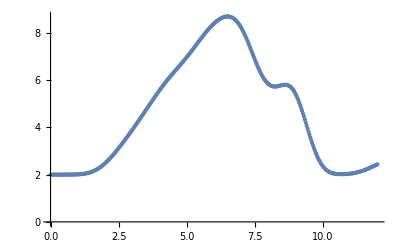

```mathematica
ListPlot[Table[{RelDisc4[[i]][[1]],RelE[RelDisc4[[i]],disk4connect]},{i,Length[RelDisc4]}]]
```

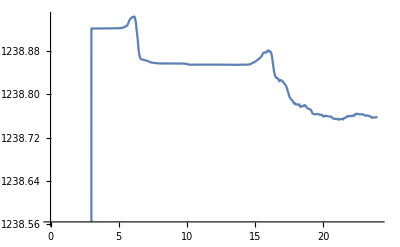

```mathematica
ListLinePlot[Table[{RelDisc4[[i]][[1]],RelE[RelDisc4[[i]],disk4connect]},{i,Length[RelDisc4]}]]
```

```mathematica
Length[RelDisc4[[2]]]
```

2

```mathematica
RelE[RelDisc4[[1]],disk4connect]
```

2.

```mathematica
RelDisc4cont=RK4[nDimtorqueDisqueCutoff[Length[disk4[[1]]],disk4connect,.001,3],50,{RelDisc4[[Length[RelDisc4]]][[1]],RelDisc4[[Length[RelDisc4]]][[1]]+24},RelDisc4[[Length[RelDisc4]]][[2]],360]
```

Part::partd: Part specification disk4⟦1⟧ is longer than depth of object.

Part::partd: Part specification Symbol⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

```mathematica
RelDisc4cont2=RK4[nDimtorqueDisqueCutoff[Length[disk4[[1]]],disk4connect,.001,3],50,{RelDisc4cont[[Length[RelDisc4cont]]][[1]],RelDisc4cont[[Length[RelDisc4cont]]][[1]]+20.2},RelDisc4cont[[Length[RelDisc4cont]]][[2]],303]
```

{{48.,{{{-0.571042,-1.30268},{-0.667287,-1.42085},{-0.546529,-1.16666},506,{-3.97258,-1.9814},{0.631484,-0.672291},{-0.42823,-0.179471}},{1}}},302,{68.2,1}}
 |  |  |  |

```mathematica
RelDisc4FFtAble=Join[Delete[RelDisc4Long,Length[RelDisc4]],Delete[RelDisc4cont2,1]]
```

{{0,{{{-0.0325874,0.0298527},{0.00546411,-0.0622607},{0.0465739,0.0607474},506,{0.324267,-0.943899},{0.39888,0.915937},{-0.913721,-0.406341}},{1}}},1022,{68.2,{1}}}
 |  |  |  |

```mathematica
Length[RelDisc4FFtAble]
```

1024

```mathematica
disk5=N[RimlessDisk[512,1]];
disk5connect=ProximalConnectDisk[disk5[[1]],.3];
(*Do[disk5[[1]][[i]]=disk5[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk5[[1]]]}] *)
RelDisc5=RK4[nDimtorqueDisqueCutoff[Length[disk5[[1]]],disk5connect,.001,1],50,{0,12},disk5,360]
```

{{0,{{{-0.0325874,0.0298527},{0.00546411,-0.0622607},{0.0465739,0.0607474},{-0.0870372,-0.0153957},{0.0833809,-0.0530401},{-0.028103,0.104542},{-0.0538924,-0.103766},{0.117415,0.0428798},496,{0.776385,-0.619318},{-0.154292,0.982077},{-0.550157,-0.829194},{0.966733,0.240033},{-0.875839,0.476494},{0.324267,-0.943899},{0.39888,0.915937},{-0.913721,-0.406341}},{1}}},359,{12.,1}}
 |  |  |  |

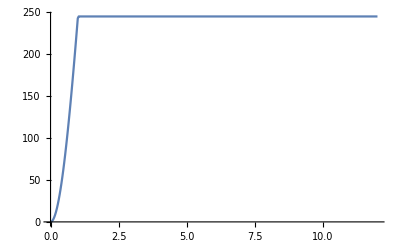

```mathematica
ListLinePlot[Table[{RelDisc5[[i]][[1]],RelE[RelDisc5[[i]],disk5connect]},{i,Length[RelDisc5]}]]
```

```mathematica
disk6=N[RimlessDisk[1024,1]];
disk6connect=ProximalConnectDisk[disk6[[1]],.2];
Do[disk6[[1]][[i]]=disk6[[1]][[i]]+{RandomReal[{-.01,.01}],RandomReal[{-.01,.01}]},{i,Length[disk6[[1]]]}]
RelDisc6=RK4[nDimtorqueDisqueCutoff[Length[disk6[[1]]],disk6connect,.0005,1],50,{0,24},disk6,720]
p5=ListAnimate[Table[ListPlot[RelDisc6[[i]][[2]][[1]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc6]}],12]
v5=ListAnimate[Table[ListPlot[RelDisc6[[i]][[2]][[2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1],{i,Length[RelDisc6]}],12]
```

$Aborted

$Aborted

ListAnimate[{},12]

ListAnimate[{},12]

```mathematica
kappa=Table[ListPlot[RelDisc3[[i]][[2]][[1]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc3]}]
```

```mathematica
ListAnimate[Table[ListPlot[RelDisc3[[i]][[2]][[1]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc3]}],12]
```

Mean::rectt: Rectangular array expected at position 1 in Mean[0.00195313].

Part::pkspec1: The expression Which[(0.00195313 «1»)/Mean[0.00195313]<2,1,Charting`CommonDump`density>10,2,True,3] cannot be used as a part specification.

```mathematica
RelDisc4Long=Join[RelDisc4,RelDisc4cont]
```

{{0,{{{-0.0325874,0.0298527},{0.00546411,-0.0622607},{0.0465739,0.0607474},{-0.0870372,-0.0153957},{0.0833809,-0.0530401},{-0.028103,0.104542},{-0.0538924,-0.103766},{0.117415,0.0428798},496,{0.776385,-0.619318},{-0.154292,0.982077},{-0.550157,-0.829194},{0.966733,0.240033},{-0.875839,0.476494},{0.324267,-0.943899},{0.39888,0.915937},{-0.913721,-0.406341}},{1}}},720,{48.,1}}
 |  |  |  |

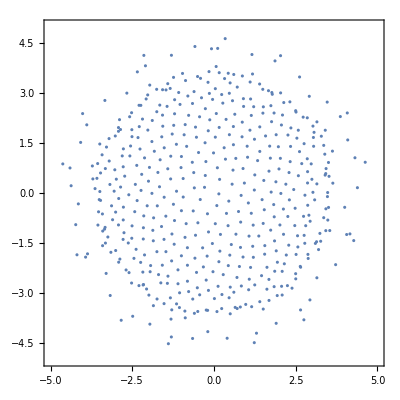

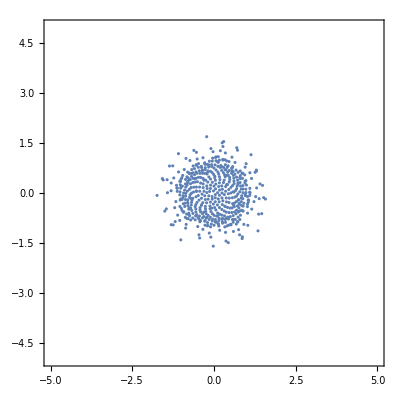

```mathematica
p4list[[241]]
p4list[[166]]
```

```mathematica
p3list=Table[ListPlot[Disc3[[i]][[2]][[1]],PlotRange->{{-5,5},{-5,5}},Frame->True,AspectRatio->1],{i,Length[RelDisc4Long]}];
```

```mathematica
p4list=Table[ListPlot[RelDisc4Long[[i]][[2]][[1]],PlotRange->{{-5,5},{-5,5}},Frame->True,AspectRatio->1],{i,Length[RelDisc4Long]}];
v4list=Table[ListPlot[RelDisc4Long[[i]][[2]][[2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1],{i,Length[RelDisc4Long]}];
```

```mathematica
p4=ListAnimate[Table[ListPlot[RelDisc4FFtAble[[i]][[2]][[1]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc4FFtAble]}],12];
v4=ListAnimate[Table[ListPlot[RelDisc4FFtAble[[i]][[2]][[2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1],{i,Length[RelDisc4FFtAble]}],12];
```

ListPlot::lpn: {{{-2.9873-2.05632×10^-6 ⅈ,0.638153+1.55687×10^-7 ⅈ},{-2.97266-8.77467×10^-7 ⅈ,1.20975+4.91917×10^-7 ⅈ},{-3.083-1.83747×10^-6 ⅈ,0.716415+3.45979×10^-7 ⅈ},{-3.0141-2.74523×10^-6 ⅈ,0.992988+9.23618×10^-7 ⅈ},{-3.03156-8.23463×10^-7 ⅈ,1.05049+8.19607×10^-8 ⅈ},«42»,{-3.23957-3.01277×10^-6 ⅈ,-0.0965104+1.08343×10^-6 ⅈ},{-2.23422-1.33897×10^-6 ⅈ,1.62472+6.80205×10^-7 ⅈ},{-3.36461-9.67147×10^-7 ⅈ,0.000506047+2.47404×10^-7 ⅈ},«462»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {{{0.0306046+3.47978×10^-8 ⅈ,-0.277329+7.16257×10^-7 ⅈ},{0.590286+4.25698×10^-7 ⅈ,0.112708-7.37166×10^-7 ⅈ},{-0.106991-9.83855×10^-7 ⅈ,-0.268567+3.23057×10^-7 ⅈ},{-0.246481-9.77162×10^-7 ⅈ,0.138548-1.30375×10^-8 ⅈ},{0.646034+3.45945×10^-7 ⅈ,-0.131114-2.08734×10^-7 ⅈ},«42»,{0.376658-1.58759×10^-6 ⅈ,-0.0681593-9.99682×10^-9 ⅈ},{0.154346-8.29472×10^-7 ⅈ,0.198517-4.35736×10^-7 ⅈ},{-0.408303-1.54224×10^-7 ⅈ,-0.487394-5.13507×10^-7 ⅈ},«462»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
A
```

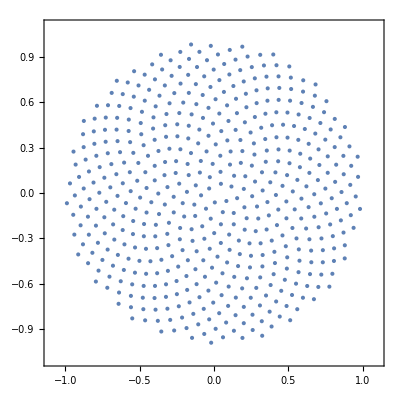

```mathematica
Show[p4list[[1]],PlotRange->{{-1.1,1.1},{-1.1,1.1}},Frame->True]
```

```mathematica
p5=ListAnimate[Table[ListPlot[RelDisc5[[i]][[2]][[1]],PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{i,Length[RelDisc5]}],12]
v5=ListAnimate[Table[ListPlot[RelDisc5[[i]][[2]][[2]],PlotRange->{{-1,1},{-1,1}},AspectRatio->1],{i,Length[RelDisc5]}],12]
```

```mathematica
Export["p4.gif",p4]
Export["v4.gif",v4]
```

p4.gif

v4.gif

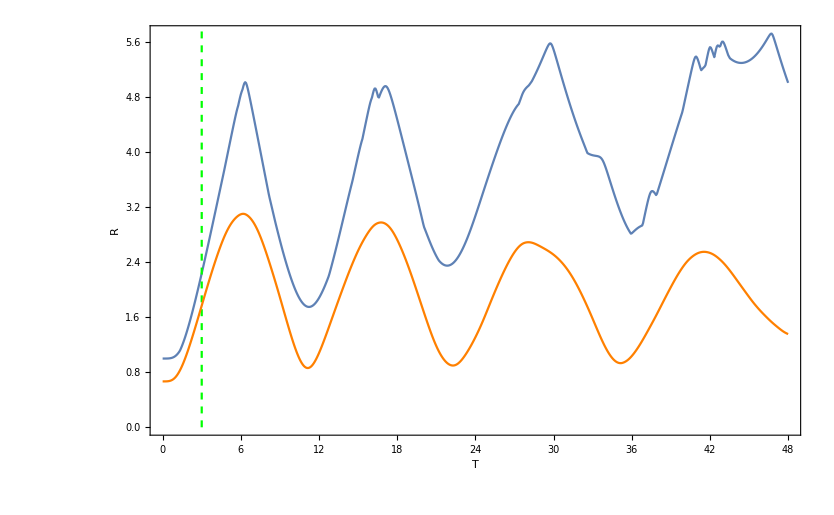

```mathematica
rvtPlotd4=ListLinePlot[Table[{RelDisc4Long[[i]][[1]],Maxr[RelDisc4Long[[i]][[2]][[1]]]},{i,Length[RelDisc4Long]}],Frame->True,FrameLabel->{"T","R"}];
rvtPlotd4avg=ListLinePlot[Table[{RelDisc4Long[[i]][[1]],Avgr[RelDisc4Long[[i]][[2]][[1]]]},{i,Length[RelDisc4Long]}],Frame->True,FrameLabel->{"T","R"},PlotStyle->Orange,PlotLabel->"Sqrt[2] Ravg"];
rvtCutoff=ParametricPlot[{3,t},{t,0,9},Frame->True,FrameLabel->{"T","MaxRadius"},PlotStyle->{Green,Dashed}];
Show[rvtPlotd4,rvtCutoff,rvtPlotd4avg]
```

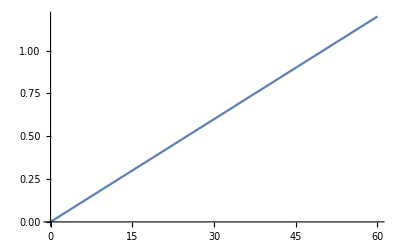

```mathematica
momvT=Table[{relkettler[[i]][[1]],RelMomentumFinder[relkettler[[i]],1.5]},{i,Length[relkettler]}];
ListLinePlot[momvT]
```

```mathematica
`
```

Part::partw: Part 17 of {0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991, 0.0159991} does not exist.

Part::partw: Part 17 of {0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991,0.0159991} does not exist.

General::stop: Further output of StyleBox[RowBox[{\"Part\", \"::\", \"partw\"}], \"MessageName\"] will be suppressed during this calculation.

```mathematica
ListAnimate[Table[ListPlot[RelDisc2[[i]][[2]][[1]],PlotRange->{{-2,2},{-2,2}},AspectRatio->1],{i,Length[RelDisc2]}],12]
```

ListPlot::lpn: {{{-0.0294015+7.38921×10^-8 ⅈ,-0.0135573+2.5876×10^-7 ⅈ},{0.0689331+5.46793×10^-8 ⅈ,-0.0235838+3.02451×10^-7 ⅈ},{-0.0190962+7.47431×10^-8 ⅈ,0.0703749+2.53278×10^-7 ⅈ},{-0.01552+6.98719×10^-8 ⅈ,-0.0825581+2.71166×10^-7 ⅈ},«43»,{-0.291355+7.90141×10^-8 ⅈ,-0.0104766+1.41739×10^-7 ⅈ},{0.245679+4.0159×10^-9 ⅈ,-0.198448+3.5713×10^-7 ⅈ},{-0.0256754+8.14717×10^-8 ⅈ,0.309446+2.00935×10^-7 ⅈ},«462»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
tettler=Table[ListLinePlot[
Table[{Cos[relkettler[[i]][[2]][[1]][[index]]],Sin[relkettler[[i]][[2]][[1]][[index]]]},{index,Length[relkettler[[i]][[2]][[1]]]}],
AspectRatio->1,PlotRange->{{-1.1,1.1},{-1.1,1.1}}],
{i,Length[relkettler]}];
```

```mathematica
Export["./disk.gif",ListAnimate[Table[ListPlot[RelDisc2[[i]][[2]][[1]],PlotRange->{{-2,2},{-2,2}},AspectRatio->1],{i,Length[RelDisc2]}],12]]
```

./disk.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./disk.gif"]]]
```

```mathematica
torkedCircle=ListAnimate[tettler,12]
```

```mathematica
awea
```

```mathematica
Export["jigglydisk.gif",ListAnimate[Table[ListPlot[RelDisc1[[i]][[2]],PlotRange->{{-2,2},{-2,2}},AspectRatio->1],{i,Length[RelDisc1]}],12]]
```

jigglydisk.gif

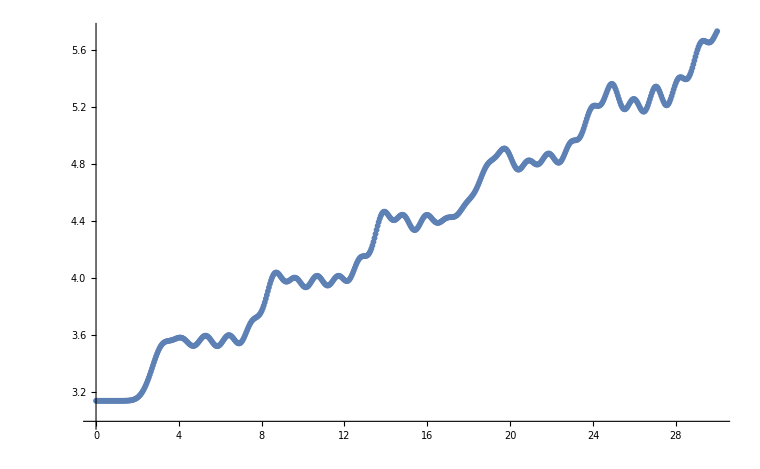

```mathematica
ettler={};
For[i=1,i≤ Length[relkettler],i++,
ettler=Append[ettler,{relkettler[[i]][[1]],relkettler[[i]][[2]][[1]][[8]]}]];
ListPlot[ettler]
```

```mathematica
(*
relRK4[f_,fpar_,{t0_,tn_},x0_,steps_,n_]:=Module[{told=t0,xold=x0,tnew,xnew,k1,k2,k3,k4,sollist={{t0,x0}},i,h,coupling_matrix=Array[mattricksy[n],{n,n}]},
h=N[(tn-t0)/steps];

For[i=0,i<steps,i++,
tnew=told+h;
(*cycle through calculating all k1?*)
k1=f[told,xold,xrm,xrp,fpar];
k2=f[told+h/2,xold+h*k1/2,xold+h*k1/2,xold+h*k1/2,fpar];
k3=f[told+h/2,xold+h*k2/2,xold+h*k2/2,xold+h*k2/2,fpar];
k4=f[told+h,xold+h*k3,xold+h*k3,xold+h*k3,fpar];
xnew=xold+h*(k1/6+k2/3+k3/3+k4/6);
sollist=Append[sollist,{tnew,xnew}];
told=tnew;
xold=xnew];
Return[sollist]]*)
```

```mathematica
k=Array[mattricksy[16],{16,16}]
l={{π/8,π/4,(3 π)/8,π/2,(5 π)/8,(3 π)/4,(7 π)/8,π,(9 π)/8,(5 π)/4,(11 π)/8,(3 π)/2,(13 π)/8,(7 π)/4,(15 π)/8,2 π},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
```

{{-2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,-2,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,-2,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,-2,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,-2,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,-2,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,-2,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,-2,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,-2,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,-2,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,-2,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,-2,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,-2,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,-2,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,-2,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-2}}

{{π/8,π/4,(3 π)/8,π/2,(5 π)/8,(3 π)/4,(7 π)/8,π,(9 π)/8,(5 π)/4,(11 π)/8,(3 π)/2,(13 π)/8,(7 π)/4,(15 π)/8,2 π},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
l.k
```

{{2 π,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 π},{-2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
pep={}
```

{}

```mathematica
Append[pep,{x,y}]
```

{{x,y}}

```mathematica
x={{1,1},{2,2},{3,3}};
con={{1,0,0},{0,1,0},{0,0,1}};
{{1},{1},{1}}.Table[x[[i]].x[[i]],{i,Length[x]}]
```

Dot::dotsh: Tensors {{1},{1},{1}} and {2,8,18} have incompatible shapes.

```mathematica
x-{1,1,1}
```

{{0,0},{1,1},{2,2}}

```mathematica
Im[{{x},{y}}]
```

{{Im[x]},{Im[y]}}

```mathematica
RimlessDisk[5,1]
```

{{{-0.329761,0.302088},{0.0552929,-0.630034},{0.471295,0.61472},{-0.880755,-0.155793},{0.843755,-0.536728}},{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}}

```mathematica
SquaredDisk[5,1]
```

{{{0,0},{0,√(π/5)},{0,-√(π/5)},{√(π/5),0},{-√(π/5),0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}}